# When should genomic imprinting affect sexual maturation?

```mathematica
Clear["Global`*"]
```

## Parameters

```mathematica
tdip={tff->1/2,tmf->1/2,tfm->1/2,tmm->1/2};
thapdip={tff->1/2,tmf->1,tfm->1/2,tmm->0};
```

Fecundity and survival functions:

```mathematica
ϕ[a_]:=(k a)^3
σ[a_]:=Exp[-μ a]
```

## Fitness expressions a_f

```mathematica
wff=1/2 tff f[afi](((1-df)s[afji])/(f[afff](1-df)s[afjff]+f[af]df s[af])+(df s[afji])/(f[af]s[af]));
```

```mathematica
wmf=1/2 tmf f[afi]((nm(1-dm))/(nf(f[afff](1-dm)+f[af]dm))+(nm dm)/(nf f[af]));
wfm=1/2 tfm nf/nm f[affm](((1-df)s[afji])/(f[affm](1-df)s[afjfm]+f[af]df s[af])+(df s[afji])/(f[af]s[af]));
wmm=1/2 tmm nf/nm f[affm]((nm(1-dm))/(nf(f[affm](1-dm)+f[af]dm))+(nm dm)/(nf f[af]));
```

## Fitness expressions a_m

```mathematica
wamff=1/2 tff ;
```

```mathematica
wammf=1/2 tmf ((nm(1-dm)s[amji])/(nf((1-dm)s[amjmf]+dm s[am]))+(nm dm s[amji])/(nf s[am]));
wamfm=1/2 tfm nf/nm f[ami]/f[ammm];
wammm=1/2 tmm nf/nm f[ami]/f[ammm]((nm(1-dm)s[amji])/(nf((1-dm)s[amjmm]+dm s[am]))+(nm dm s[amji])/(nf s[am]));
```

## Reproductive values, class frequencies

Demographical model of homogeneous population

```mathematica
A={{wff,wfm},{wmf,wmm}}/.{affm->af,afff->af,afjfm->af,afjff->af,afji->af,afi->af}//Simplify
```

{{tff/2,(nf tfm)/(2 nm)},{(nm tmf)/(2 nf),tmm/2}}

```mathematica
evals=Simplify[Eigenvalues[A]]
```

{1/4 (tff+tmm-√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)),1/4 (tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2))}

```mathematica
classfreqs=Simplify[Eigenvectors[1/evals[[2]] A]]
```

{{-(nf (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1},{(nf (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1}}

```mathematica
repvals=Simplify[Eigenvectors[1/evals[[2]] Transpose[A]]]
```

{{-(nm (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1},{(nm (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1}}

### Diplodiploidy

Stable class frequencies

```mathematica
udipR=Simplify[classfreqs[[2]]/Total[classfreqs[[2]]]/.tdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
udip={uf->udipR[[1]],um->udipR[[2]]};
```

Individual reproductive values

```mathematica
vdipR=Simplify[repvals[[2]]/Total[udipR.repvals[[2]]]/.tdip]
```

{(nf+nm)/(2 nf),(nf+nm)/(2 nm)}

```mathematica
vdip={vf->vdipR[[1]],vm->vdipR[[2]]};
```

Class reproductive values

```mathematica
cdip={cf->vf uf,cm->vm um}/.vdip/.udip
```

{cf→1/2,cm→1/2}

### Haplodiploidy

```mathematica
uhapdipR=Simplify[classfreqs[[2]]/Total[classfreqs[[2]]]/.thapdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
uhapdip={uf->uhapdipR[[1]],um->uhapdipR[[2]]};
```

Individual reproductive values

```mathematica
vhapdipR=Simplify[repvals[[2]]/Total[uhapdipR.repvals[[2]]]/.thapdip]
```

{(2 (nf+nm))/(3 nf),(nf+nm)/(3 nm)}

```mathematica
vhapdip={vf->vhapdipR[[1]],vm->vhapdipR[[2]]};
```

Class reproductive values

```mathematica
chapdip={cf->vf uf,cm->vm um}/.vhapdip/.uhapdip
```

{cf→2/3,cm→1/3}

## Selection gradient on a_f

```mathematica
Wfaf=wff+vm/vf wmf;
Wmaf=wmm+vf/vm wfm;
```

```mathematica
selgradaf=cf(D[Wfaf,afi]rfi+D[Wfaf,afji]rfkidf+D[Wfaf,afff]rff+D[Wfaf,afjff]rflocjf)+cm(D[Wmaf,afji]rmkidf+D[Wmaf,affm]rmf+D[Wmaf,afjfm]rmlocjf)/.{afi->af,afji->af,afff->af,afjff->af,affm->af,afjfm->af}//Simplify
```

1/(2 nf nm vf vm f[af] s[af])(-(cf nm vm (nf ((-1+df)^2 rff-rfi) tff vf+nm ((-1+dm)^2 rff-rfi) tmf vm)+cm nf rmf vf (-2 df nf tfm vf+df^2 nf tfm vf+(-2+dm) dm nm tmm vm)) s[af] f'[af]+nf vf (cm nf (rmkidf-(-1+df)^2 rmlocjf) tfm vf+cf nm (rfkidf-(-1+df)^2 rflocjf) tff vm) f[af] s'[af])

## Selection gradient on a_m

```mathematica
Wfam=wamff+vm/vf wammf;
Wmam=wammm+vf/vm wamfm;
```

```mathematica
selgradam=cf(D[Wfam,amji]rfkidm+D[Wfam,amjmf]rflocjm)+cm(D[Wmam,ami]rmi+D[Wmam,amji]rmkidm+D[Wmam,ammm]rmm+D[Wmam,amjmm]rmlocjm)/.{amji->am,amjmf->am,ami->am,ammm->am,amjmm->am}//Simplify
```

(cm nf (rmi-rmm) vf (nf tfm vf+nm tmm vm) s[am] f'[am]-nm vm (cm nf (-rmkidm+(-1+dm)^2 rmlocjm) tmm vf+cf nm (-rfkidm+(-1+dm)^2 rflocjm) tmf vm) f[am] s'[am])/(2 nf nm vf vm f[am] s[am])

## Relatedness

### Diplodiploidy

#### Coefficients of consanguinity

```mathematica
hf=1-df;
hm=1-dm;
```

```mathematica
Qdip={QffJ==QmmJ==QfmJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm+1/4(1/nm Qm+(nm-1)/nm Qmm),
Qf==1/2(1+Qfm),
Qf==Qm,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsoldip=Solve[Qdip,{QffJ,QmmJ,QfmJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients

```mathematica
rdip={
rfi->Qf,
rmi->Qm,
rff->Qff,
rmf->Qmf,
rmm->Qmm,
rmkidf->Qf,
rmkidm->Qm,
rfkidm->Qm,
rfkidf->Qf,
rflocjf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rflocjm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rmlocjf->1/2(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf,
rmlocjm->1/2(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf
}/.Qsoldip;
```

```mathematica
rdipMI={
rfi->Qf,
rmi->Qm,
rmf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rmm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rfm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rff->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rmkidf->Qfm,
rmkidm->Qfm,
rfkidf->1,
rfkidm->1,
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsoldip;
```

```mathematica
rdipPI={
rfi->Qf,
rmi->Qm,
rmf->1/2(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qfm,
rmm->1/2(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qfm,
rfm->1/2(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qfm,
rff->1/2(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qfm,
rmkidf->1,
rmkidm->1,
rfkidf->Qfm,
rfkidm->Qfm,
rflocjf->Qfm,
rflocjm->Qfm,
rmlocjf->1/nm Qm+(nm-1)/nm Qmm,
rmlocjm->1/nm Qm+(nm-1)/nm Qmm}/.Qsoldip;
```

### Haplodiploidy

#### Coefficients of consanguinity

```mathematica
Qhapdip={QffJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm+1/4(1/nm Qm+(nm-1)/nm Qmm),
QfmJ==QmfJ==1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
QmmJ==1/nf Qf+(nf-1)/nf Qff,
Qf==1/2(1+Qfm),
Qm==1,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsolhapdip=Solve[Qhapdip,{QffJ,QmmJ,QfmJ,QmfJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients

```mathematica
rhapdip={
rfi->Qf,
rmi->Qm,
rff->Qff,
rmf->Qmf,
rfm->Qmf,
rmm->Qmm,
rmkidf->Qf,
rmkidm->Qfm,
rfkidm->Qm,
rfkidf->Qf,
rflocjf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->1/2(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf,
rmlocjm->Qmf
}/.Qsolhapdip;
```

```mathematica
rhapdipMI={
rfi->Qf,
rmi->Qm,
rmf->1/nf Qf+(nf-1)/nf Qff,
rmm->1/nf Qf+(nf-1)/nf Qff,
rfm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rff->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 Qfm,
rmkidf->Qfm,
rmkidm->Qfm,
rfkidf->1,
rfkidm->1,
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsolhapdip;
```

```mathematica
rhapdipPI={
rfi->Qf,
rmi->Qm,
rmf->Qmf,
rmm->Qmm,
rfm->Qfm,
rff->1/2(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qfm,
rmkidf->1,
rmkidm->Qfm,
rfkidf->Qfm,
rfkidm->1,
rflocjf->Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->1/nm Qm+(nm-1)/nm Qmm,
rmlocjm->Qmf}/.Qsolhapdip;
```

## Results diplodiploidy

```mathematica
ans[{nfs_,nms_},{dfs_,dms_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdip/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks},{{af,1.5},{am,1.5}}]
```

```mathematica
ansMI[{nfs_,nms_},{dfs_,dms_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipMI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks},{{af,1.5},{am,1.5}}]
```

```mathematica
ansPI[{nfs_,nms_},{dfs_,dms_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipPI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks},{{af,1.5},{am,1.5}}]
```

```mathematica
ans[{2,2},{0.9,0.1},{1,1/3}]
```

{af→3.05206,am→3.}

```mathematica
a1=Table[{{dm,af},{dm,am}}/.ans[{2,2},{0.5,dm},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,3.39706},{0.,3.}},{{0.05,3.41446},{0.05,3.}},{{0.1,3.42543},{0.1,3.}},{{0.15,3.43101},{0.15,3.}},{{0.2,3.43204},{0.2,3.}},{{0.25,3.42922},{0.25,3.}},{{0.3,3.42313},{0.3,3.}},{{0.35,3.41428},{0.35,3.}},{{0.4,3.40308},{0.4,3.}},{{0.45,3.38988},{0.45,3.}},{{0.5,3.375},{0.5,3.}},{{0.55,3.35871},{0.55,3.}},{{0.6,3.34126},{0.6,3.}},{{0.65,3.32284},{0.65,3.}},{{0.7,3.30366},{0.7,3.}},{{0.75,3.28388},{0.75,3.}},{{0.8,3.26366},{0.8,3.}},{{0.85,3.24313},{0.85,3.}},{{0.9,3.22244},{0.9,3.}},{{0.95,3.20171},{0.95,3.}},{{1.,3.18103},{1.,3.}}}

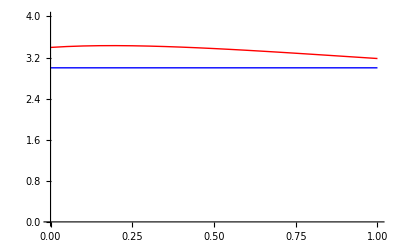

```mathematica
p1=ListLinePlot[Transpose[a1],PlotRange->{0,4},PlotStyle->{Red,Blue}]
```

```mathematica
a1MI=Table[{{dm,af},{dm,am}}/.ansMI[{2,1},{0.25,dm},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,3.},{0.,3.}},{{0.05,3.24855},{0.05,2.65047}},{{0.1,3.45725},{0.1,2.42947}},{{0.15,3.63197},{0.15,2.28066}},{{0.2,3.7775},{0.2,2.17656}},{{0.25,3.89781},{0.25,2.10219}},{{0.3,3.99624},{0.3,2.04867}},{{0.35,4.07557},{0.35,2.01043}},{{0.4,4.1382},{0.4,1.98379}},{{0.45,4.18613},{0.45,1.96622}},{{0.5,4.22112},{0.5,1.95595}},{{0.55,4.24467},{0.55,1.95167}},{{0.6,4.25808},{0.6,1.95242}},{{0.65,4.26249},{0.65,1.9575}},{{0.7,4.25889},{0.7,1.96633}},{{0.75,4.24818},{0.75,1.97849}},{{0.8,4.23111},{0.8,1.99366}},{{0.85,4.20838},{0.85,2.01156}},{{0.9,4.1806},{0.9,2.032}},{{0.95,4.14832},{0.95,2.05479}},{{1.,4.11203},{1.,2.07983}}}

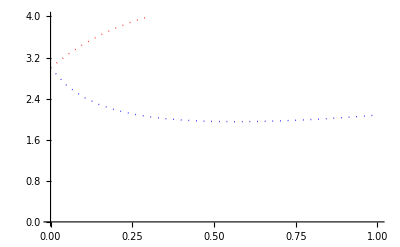

```mathematica
p1MI=ListLinePlot[Transpose[a1MI],PlotRange->{0,4},PlotStyle->{{Red,Dotted},{Blue,Dotted}}]
```

```mathematica
a1PI=Table[{{dm,af},{dm,am}}/.ansPI[{2,1},{0.25,dm},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,3.},{0.,3.}},{{0.05,3.3648},{0.05,2.36663}},{{0.1,3.6797},{0.1,2.03571}},{{0.15,3.95143},{0.15,1.83566}},{{0.2,4.18552},{0.2,1.70425}},{{0.25,4.38655},{0.25,1.61345}},{{0.3,4.55836},{0.3,1.54881}},{{0.35,4.70415},{0.35,1.50212}},{{0.4,4.82667},{0.4,1.46841}},{{0.45,4.92824},{0.45,1.44445}},{{0.5,5.01087},{0.5,1.42813}},{{0.55,5.0763},{0.55,1.41796}},{{0.6,5.12602},{0.6,1.41291}},{{0.65,5.16135},{0.65,1.41223}},{{0.7,5.18343},{0.7,1.41539}},{{0.75,5.19328},{0.75,1.42201}},{{0.8,5.19178},{0.8,1.4318}},{{0.85,5.17973},{0.85,1.44459}},{{0.9,5.15784},{0.9,1.46025}},{{0.95,5.12672},{0.95,1.47872}},{{1.,5.08696},{1.,1.5}}}

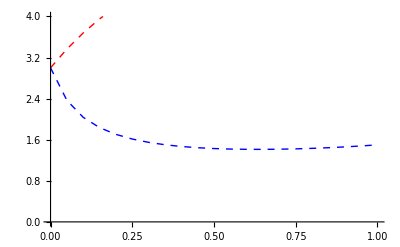

```mathematica
p1PI=ListLinePlot[Transpose[a1PI],PlotRange->{0,4},PlotStyle->{{Red,Dashed},{Blue,Dashed}}]
```

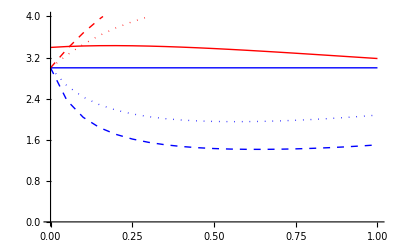

```mathematica
Show[{p1,p1MI,p1PI}]
```

## Results haplodiploidy

```mathematica
anshap[{nfs_,nms_},{dfs_,dms_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdip/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapMI[{nfs_,nms_},{dfs_,dms_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipMI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapPI[{nfs_,nms_},{dfs_,dms_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipPI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks},{{af,1.5},{am,1.5}}]
```

```mathematica
ans[{4,4},{0.9,0.1},{1,1/3}]
```

{af→3.02766,am→3.}

```mathematica
a1h=Table[{{dm,af},{dm,am}}/.anshap[{2,2},{0.5,dm},{1,0.3333}],{dm,0,1,0.05}]
```

{{{0.,3.41827},{0.,3.}},{{0.05,3.41808},{0.05,3.}},{{0.1,3.41671},{0.1,3.}},{{0.15,3.41428},{0.15,3.}},{{0.2,3.41088},{0.2,3.}},{{0.25,3.40661},{0.25,3.}},{{0.3,3.40155},{0.3,3.}},{{0.35,3.3958},{0.35,3.}},{{0.4,3.38941},{0.4,3.}},{{0.45,3.38246},{0.45,3.}},{{0.5,3.375},{0.5,3.}},{{0.55,3.36708},{0.55,3.}},{{0.6,3.35876},{0.6,3.}},{{0.65,3.35007},{0.65,3.}},{{0.7,3.34104},{0.7,3.}},{{0.75,3.33172},{0.75,3.}},{{0.8,3.32211},{0.8,3.}},{{0.85,3.31225},{0.85,3.}},{{0.9,3.30215},{0.9,3.}},{{0.95,3.29181},{0.95,3.}},{{1.,3.28125},{1.,3.}}}

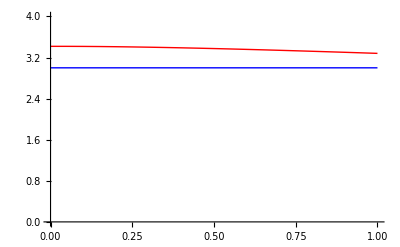

```mathematica
p1h=ListLinePlot[Transpose[a1h],PlotRange->{0,4},PlotStyle->{Red,Blue}]
```

```mathematica
Show[p1,p1h]
```

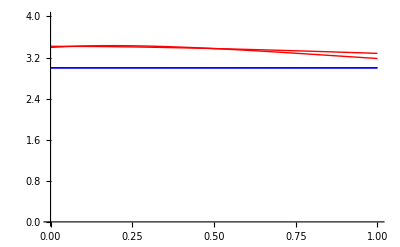

```mathematica
a1MIh=Table[{{dm,af},{dm,am}}/.anshapMI[{2,1},{0.5,dm},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,3.24398},{0.,3.}},{{0.05,3.31356},{0.05,2.86679}},{{0.1,3.37744},{0.1,2.75345}},{{0.15,3.43591},{0.15,2.65629}},{{0.2,3.48926},{0.2,2.57256}},{{0.25,3.53777},{0.25,2.5001}},{{0.3,3.5817},{0.3,2.43724}},{{0.35,3.62126},{0.35,2.38265}},{{0.4,3.65668},{0.4,2.33526}},{{0.45,3.68817},{0.45,2.29422}},{{0.5,3.71591},{0.5,2.25882}},{{0.55,3.74008},{0.55,2.2285}},{{0.6,3.76086},{0.6,2.20278}},{{0.65,3.7784},{0.65,2.18128}},{{0.7,3.79284},{0.7,2.16369}},{{0.75,3.80432},{0.75,2.14976}},{{0.8,3.81298},{0.8,2.13926}},{{0.85,3.81894},{0.85,2.13205}},{{0.9,3.82232},{0.9,2.128}},{{0.95,3.82321},{0.95,2.12701}},{{1.,3.82174},{1.,2.12903}}}

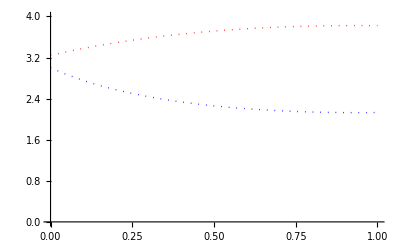

```mathematica
p1MIh=ListLinePlot[Transpose[a1MIh],PlotRange->{0,4},PlotStyle->{{Red,Dotted},{Blue,Dotted}}]
```

```mathematica
a1PIh=Table[{{dm,af},{dm,am}}/.anshapPI[{2,1},{0.5,dm},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,1.79348},{0.,3.}},{{0.05,1.96904},{0.05,3.}},{{0.1,2.13525},{0.1,3.}},{{0.15,2.29209},{0.15,3.}},{{0.2,2.43951},{0.2,3.}},{{0.25,2.5775},{0.25,3.}},{{0.3,2.70602},{0.3,3.}},{{0.35,2.82506},{0.35,3.}},{{0.4,2.93458},{0.4,3.}},{{0.45,3.03457},{0.45,3.}},{{0.5,3.125},{0.5,3.}},{{0.55,3.20586},{0.55,3.}},{{0.6,3.27712},{0.6,3.}},{{0.65,3.33878},{0.65,3.}},{{0.7,3.3908},{0.7,3.}},{{0.75,3.43319},{0.75,3.}},{{0.8,3.46592},{0.8,3.}},{{0.85,3.48898},{0.85,3.}},{{0.9,3.50235},{0.9,3.}},{{0.95,3.50603},{0.95,3.}},{{1.,3.5},{1.,3.}}}

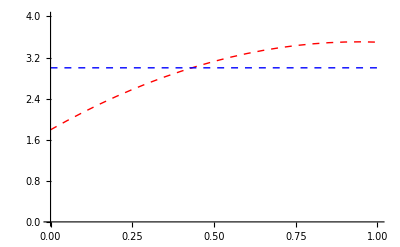

```mathematica
p1PIh=ListLinePlot[Transpose[a1PIh],PlotRange->{0,4},PlotStyle->{{Red,Dashed},{Blue,Dashed}}]
```

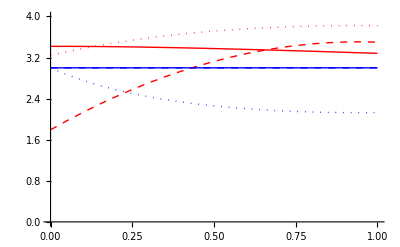

```mathematica
Show[{p1h,p1MIh,p1PIh}]
```